```mathematica
data=Table[{y,-x},{x,-3,3,0.2},{y,-3,3,0.2}];
```

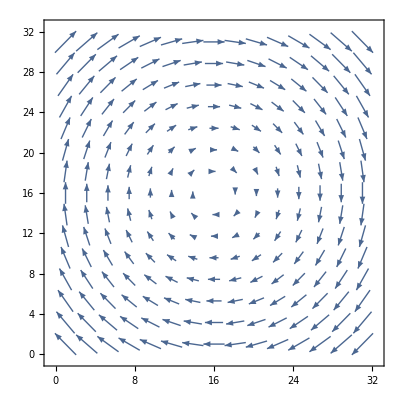

```mathematica
ListVectorPlot@data
```

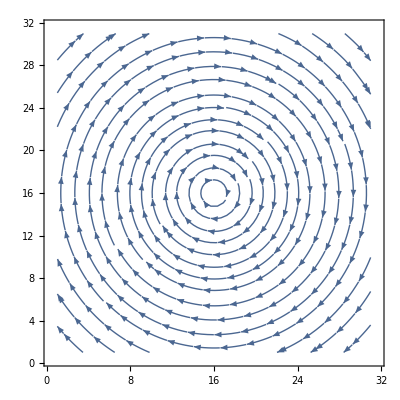

```mathematica
ListStreamPlot@data
```

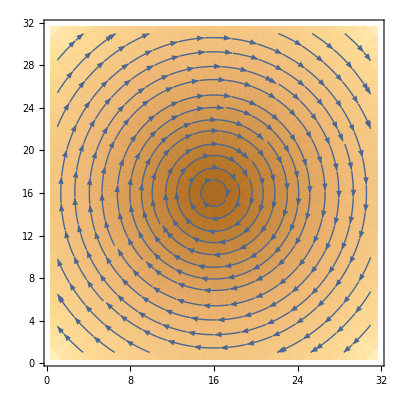

```mathematica
ListStreamDensityPlot[data]
```

```mathematica
data=Import["/home/levesque/Recherche/src/laboetie/output/vel-field_central.dat"];
```

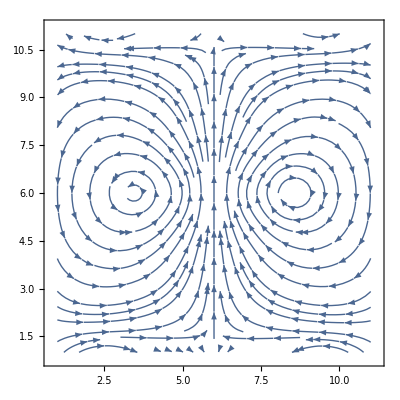

```mathematica
ListStreamPlot[data,ColorFunction->"Temperature"]
```

-Graphics-

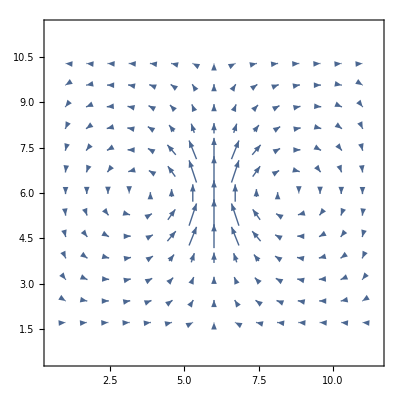

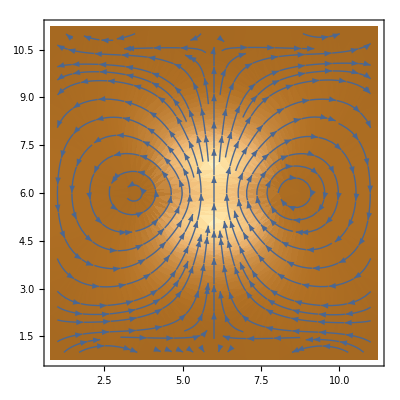

```mathematica
data=Import["/home/levesque/Recherche/src/laboetie/output/vel-field_central.dat"]
ListStreamPlot[data]
ListVectorPlot[data]
ListStreamDensityPlot[data]
```

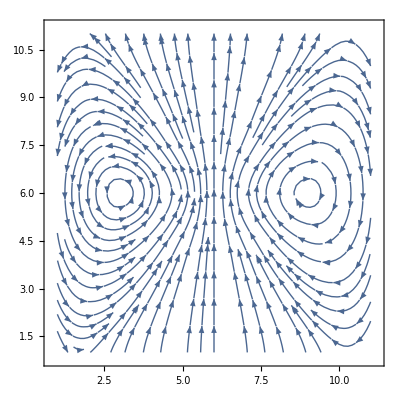

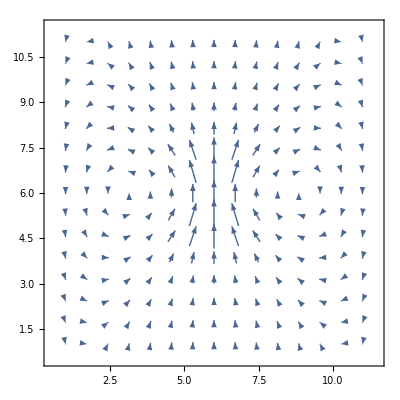

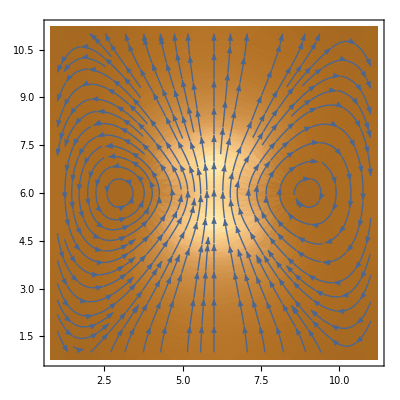

```mathematica
data=Import["/home/levesque/Recherche/src/laboetie/output/vel-field_central.dat"];
ListStreamPlot[data]
ListVectorPlot[data]
ListStreamDensityPlot[data]
```

```mathematica
data=Import["/home/levesque/Recherche/src/laboetie/output/vel-field_central.dat","Table"];
```

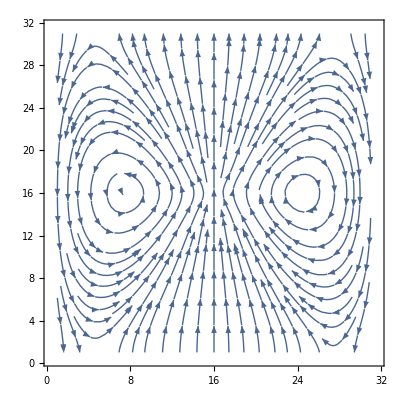

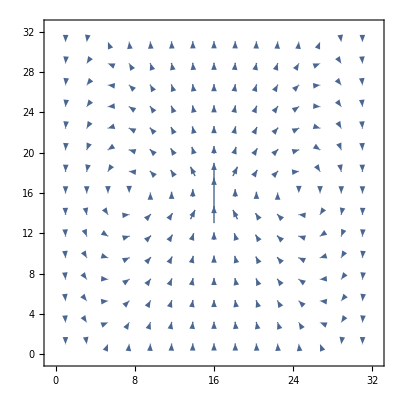

```mathematica
ListStreamPlot[data]
ListVectorPlot[data]
```

```mathematica
fext=Import["/home/levesque/Recherche/src/laboetie/output/f_ext-field.dat","Table"];
```

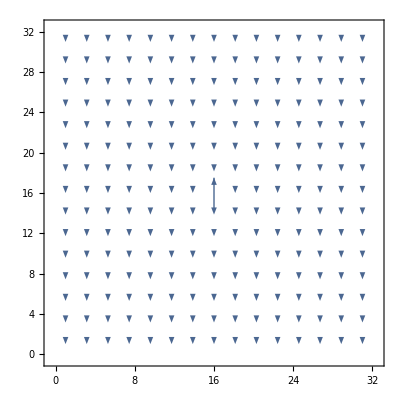

```mathematica
ListVectorPlot[fext]
```

```mathematica
ListStreamPlot[data]
```

-Graphics-

```mathematica
v=Import["/home/levesque/Recherche/src/laboetie/output/v_centralnode.dat","Table"]
```

{{0.},{-1.67842×10^-9},{2.31154×10^-6},{5.02343×10^-6},{7.54044×10^-6},{9.70557×10^-6},3870,{0.0000324151},{0.0000324151},{0.0000324151},{0.0000324151},{0.0000324151},{0.0000324151}}
 |  |  |  |

```mathematica
vz=Transpose[v][[4]];
```

Part::partw: Part 4 of {{0., -1.67842×10^-9, 2.31154×10^-6, 5.02343×10^-6, 7.54044×10^-6, 9.70557×10^-6, 0.0000115225, « 37 », 0.0000259598, 0.0000260602, 0.0000261573, 0.0000262513, 0.0000263425, 0.0000264309, « 3832 »}} does not exist.

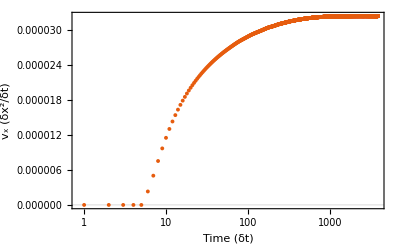

```mathematica
ListLogLinearPlot[vz,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"Time (δt)","v_x (δx^2/δt)"}]
```

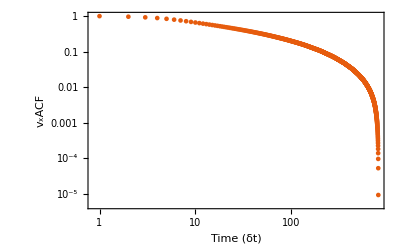

```mathematica
acfvz=CorrelationFunction[vz,{0,Length[vz]-1}];
ListLogLogPlot[acfvz,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"Time (δt)","v_xACF"}]
```

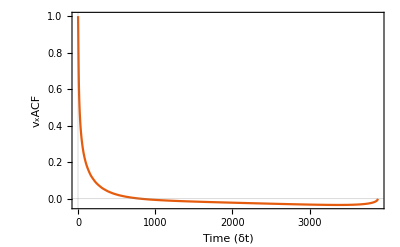

```mathematica
ListLinePlot[acfvz,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"Time (δt)","v_xACF"}]
```

```mathematica
f=Interpolation@acfvz
```

InterpolatingFunction[{{1., 3885.}}, <>]

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

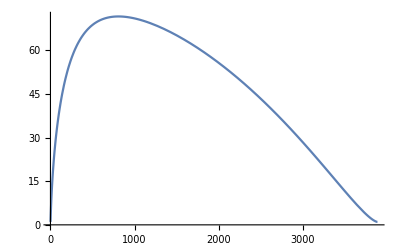

```mathematica
Plot[Integrate[f[t],{t,0,x}],{x,1,Length@acfvz},PlotRange->All]
```